Dynamic visualization of eigenvalues of 2x2 Hermitian matrix, as sketched in lecture 20, plus some plots with specific values.

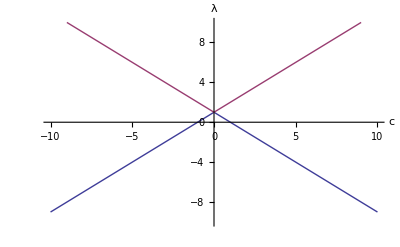
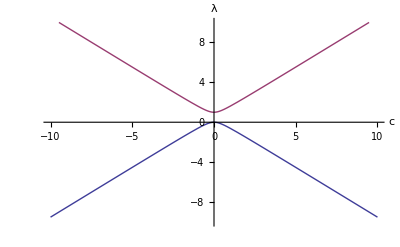
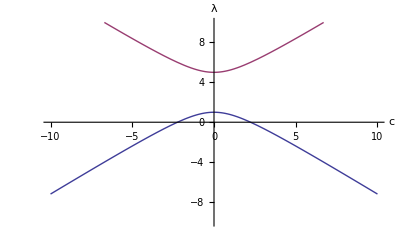
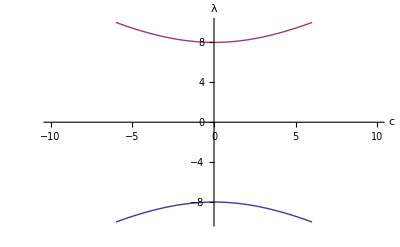
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ClearAll[a, b, c, e, h, x, y, z, p, l1, l2] ;

(* declare various variables as Real and > 0 *)
$Assumptions=And@@(#>0&)/@{a, b};

h= {{a, c}, {Conjugate[c], b}} ;

e = Eigenvalues[ h ] // Simplify ;

l1[x_,y_,z_] = (e // First) /. {a -> x, b -> y, c -> z} ;
l2[x_,y_,z_] = (e // Last) /. {a -> x, b -> y, c -> z} ;

Manipulate[ 
(*Graphics[{*)
Plot[{l1[a,b,c],l2[a,b,c]}, {c,-10,10}, PlotRange -> {{-20, 20}, {-20, 20}},
AxesLabel->{c, "λ"}],
{{a,1}, -10, 10},
{{b, 1}, -10, 10}
]

p = Plot[{l1[#1,#2,c],l2[#1,#2,c]}, {c,-10,10}, PlotRange -> {{-10,10}, {-10, 10}},
AxesLabel->{c, "λ"}] & @@@ {{1,1}, {1,0}, {1, 5}, {5,1},{-8, 8}}
```

```mathematica
peeters`exportForLatex["lecture20Fig3", p // First]
peeters`exportForLatex["lecture20Fig4", p [[2]]]
peeters`exportForLatex["lecture20Fig5", p[[3]] ]
peeters`exportForLatex["lecture20Fig6", p // Last ]
```

{lecture20Fig3.eps,lecture20Fig3pn.png}

{lecture20Fig4.eps,lecture20Fig4pn.png}

{lecture20Fig5.eps,lecture20Fig5pn.png}

{lecture20Fig6.eps,lecture20Fig6pn.png}